```mathematica
SetDirectory[NotebookDirectory[]];
```

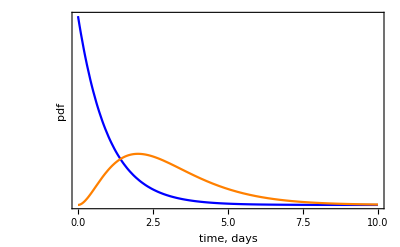

```mathematica
λ = 1;
g1=Plot[{PDF[ExponentialDistribution[1],x],PDF[TransformedDistribution[u+v+w,{u\[Distributed]ExponentialDistribution[λ],v\[Distributed]ExponentialDistribution[λ],w\[Distributed]ExponentialDistribution[λ]}],x]},{x,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"time, days","pdf"},BaseStyle->Medium,PlotStyle->{Blue,Orange}]
```

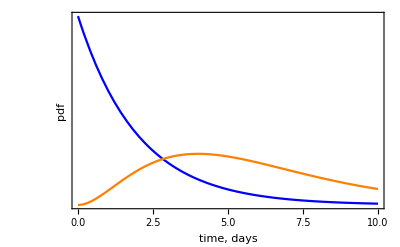

```mathematica
λ = 0.5;
g2=Plot[{PDF[ExponentialDistribution[λ],x],PDF[TransformedDistribution[u+v+w,{u\[Distributed]ExponentialDistribution[λ],v\[Distributed]ExponentialDistribution[λ],w\[Distributed]ExponentialDistribution[λ]}],x]},{x,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"time, days","pdf"},BaseStyle->Medium,PlotStyle->{Blue,Orange}]
```

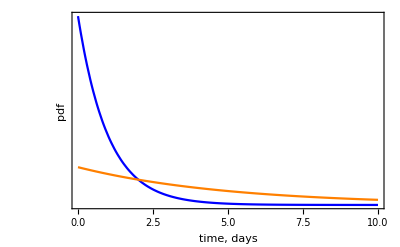

```mathematica
λ = 1;
g3=Plot[{PDF[ExponentialDistribution[λ],x],PDF[GammaDistribution[1,5],x]},{x,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"time, days","pdf"},BaseStyle->Medium,PlotStyle->{Blue,Orange,Red}]
```

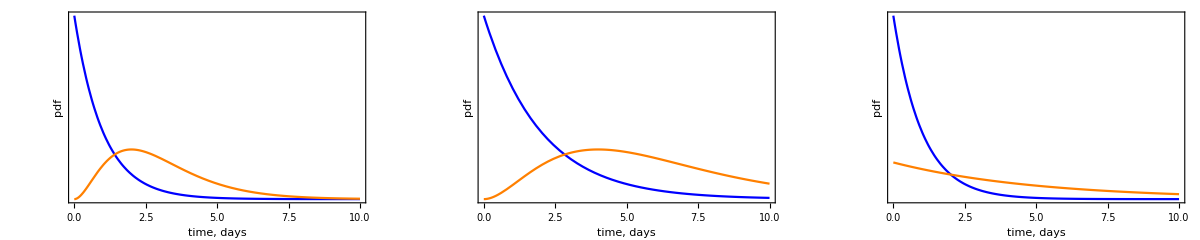

```mathematica
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->1200]
```

```mathematica
Export["Distributions_gammaLottery.pdf",gFinal]
```

Distributions_gammaLottery.pdf